# A-Coefficients

Generates tables of A-coefficients for an alpha particle traversing a DT plasma.

## D to T ratio

```mathematica
r=1;
```

## Densities and temperatures

Electron and ion number densities in cm^-3

```mathematica
ne=10^26;
```

```mathematica
nD=r*ne/(1+r);
```

```mathematica
nT=ne/(1+r);
```

Electron and ion temperatures in keV

```mathematica
Te=15.8;
```

```mathematica
TI=15.8;
```

## m_i, ϵ_i, and function definitions

All masses are in  keV.

```mathematica
me=511;
```

```mathematica
mD=1.8756*10^6;
```

```mathematica
mT=2.8089*10^6;
```

```mathematica
malpha=3.7273*10^6;
```

```mathematica
epse=2.664*10^(-5)*me/Te
```

0.000861585

```mathematica
epsD=2.664*10^(-5)*mD/TI
```

3.1624

```mathematica
epsT=2.664*10^(-5)*mT/TI
```

4.73602

```mathematica
daw[t_]:=(Sqrt[Pi]/2)*Exp[-t^2]*Erfi[t]
```

```mathematica
F1[u_]:=1-2*Sqrt[epse]*u*daw[Sqrt[epse]*u]+(nD/ne)*(Te/TI)*(1-2*Sqrt[epsD]*u*daw[Sqrt[epsD]*u])+(nT/ne)*(Te/TI)*(1-2*Sqrt[epsT]*u*daw[Sqrt[epsT]*u])
```

```mathematica
F2[u_]:=Pi*u*(Sqrt[epse/Pi]*Exp[-epse*u^2]+(nD/ne)*(Te/TI)*Sqrt[epsD/Pi]*Exp[-epsD*u^2]+(nT/ne)*(Te/TI)*Sqrt[epsT/Pi]*Exp[-epsT*u^2])
```

## A-electron

```mathematica
AeC[s_]:=4*2.608*10^(-23)*(ne/Te)*Sqrt[epse/Pi]*s*NIntegrate[x^2*Exp[-epse*s^2*x^2]*(2*Log[(1-x^2)/x^2]-(1/2)*Log[F1[s*x]^2+F2[s*x]^2]-(F1[s*x]/F2[s*x])*Arg[F1[s*x]+I*F2[s*x]]-2*Log[2*6.13*10^(-15)*Sqrt[ne/Te]*(1/Te)*(1+me/malpha)]+4*(1-EulerGamma)),{x,0,1}]
```

```mathematica
AeQ[s_]:=-4*2.608*10^(-23)*(ne/Te)*Sqrt[1/(4*Pi*epse)]*(1/s)*NIntegrate[(1/x)*(Re[PolyGamma[0,1+I*(2/x)]+PolyGamma[0,1-I*(2/x)]]/2-Log[2/x])*(Exp[-epse*(s-x)^2]*(1-1/(2*epse*s*x))+Exp[-epse*(s+x)^2]*(1+1/(2*epse*s*x))),{x,0,Infinity}]
```

```mathematica
Ae0[s_]:=AeC[s]+AeQ[s]
```

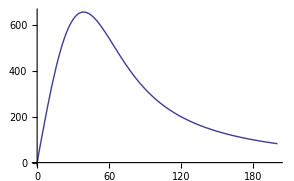

```mathematica
Plot[Ae0[s],{s,0.01,200}]
```

```mathematica
tableAe0=Prepend[Table[{s,Ae0[s]},{s,0.1,10,0.1}],{0,0}];
```

```mathematica
Interpolation[tableAe0,InterpolationOrder->3]
```

InterpolatingFunction[{{0.,10.}},<>]

```mathematica
Ae[s_]:=Evaluate[Interpolation[tableAe0]][s]
```

## A-deuteron

```mathematica
ADC[s_]:=4*2.608*10^(-23)*(nD/TI)*Sqrt[epsD/Pi]*s*NIntegrate[x^2*Exp[-epsD*s^2*x^2]*(2*Log[(1-x^2)/x^2]-(1/2)*Log[F1[s*x]^2+F2[s*x]^2]-(F1[s*x]/F2[s*x])*Arg[F1[s*x]+I*F2[s*x]]-2*Log[2*6.13*10^(-15)*Sqrt[ne/Te]*(1/TI)*(1+mD/malpha)]+4*(1-EulerGamma)),{x,0,1}]
```

```mathematica
ADQ[s_]:=-4*2.608*10^(-23)*(nD/TI)*Sqrt[1/(4*Pi*epsD)]*(1/s)*NIntegrate[(1/x)*(Re[PolyGamma[0,1+I*(2/x)]+PolyGamma[0,1-I*(2/x)]]/2-Log[2/x])*(Exp[-epsD*(s-x)^2]*(1-1/(2*epsD*s*x))+Exp[-epsD*(s+x)^2]*(1+1/(2*epsD*s*x))),{x,0,Infinity}]
```

```mathematica
AD0[s_]:=ADC[s]+ADQ[s]
```

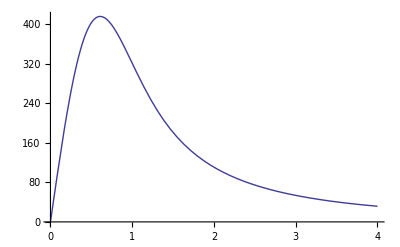

```mathematica
Plot[AD0[s],{s,0.001,4}]
```

```mathematica
tableAD0=Prepend[Table[{s,AD0[s]},{s,0.1,10,0.1}],{0,0}];
```

```mathematica
Interpolation[tableAD0,InterpolationOrder->3]
```

InterpolatingFunction[{{0.,10.}},<>]

```mathematica
AD[s_]:=Evaluate[Interpolation[tableAD0]][s]
```

## A-triton

```mathematica
ATC[s_]:=4*2.608*10^(-23)*(nT/TI)*Sqrt[epsT/Pi]*s*NIntegrate[x^2*Exp[-epsT*s^2*x^2]*(2*Log[(1-x^2)/x^2]-(1/2)*Log[F1[s*x]^2+F2[s*x]^2]-(F1[s*x]/F2[s*x])*Arg[F1[s*x]+I*F2[s*x]]-2*Log[2*6.13*10^(-15)*Sqrt[ne/Te]*(1/TI)*(1+mT/malpha)]+4*(1-EulerGamma)),{x,0,1}]
```

```mathematica
ATQ[s_]:=-4*2.608*10^(-23)*(nT/TI)*Sqrt[1/(4*Pi*epsT)]*(1/s)*NIntegrate[(1/x)*(Re[PolyGamma[0,1+I*(2/x)]+PolyGamma[0,1-I*(2/x)]]/2-Log[2/x])*(Exp[-epsT*(s-x)^2]*(1-1/(2*epsT*s*x))+Exp[-epsT*(s+x)^2]*(1+1/(2*epsT*s*x))),{x,0,Infinity}]
```

```mathematica
AT0[s_]:=ATC[s]+ATQ[s]
```

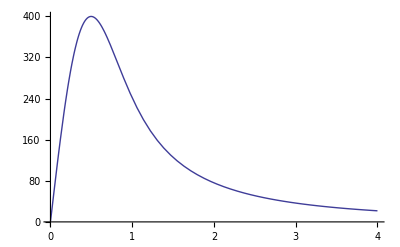

```mathematica
Plot[AT0[s],{s,0.001,4}]
```

```mathematica
tableAT0=Prepend[Table[{s,AT0[s]},{s,0.1,10,0.1}],{0,0}];
```

```mathematica
Interpolation[tableAT0,InterpolationOrder->3]
```

InterpolatingFunction[{{0.,10.}},<>]

```mathematica
AT[s_]:=Evaluate[Interpolation[tableAT0]][s]
```

## A-ion

```mathematica
tableAI0=Table[{s,AD[s]+AT[s]},{s,0,10,0.1}];
```

```mathematica
Interpolation[tableAI0,InterpolationOrder->3]
```

InterpolatingFunction[{{0.,10.}},<>]

```mathematica
AI[s_]:=Evaluate[Interpolation[tableAI0]][s]
```

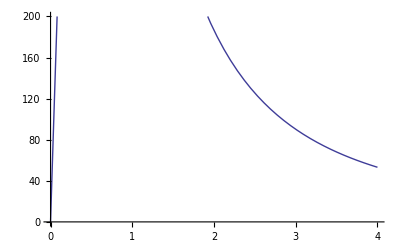

```mathematica
Plot[AI[s],{s,0,4},PlotRange->{{0,4},{0,200}}]
```

## A-total

```mathematica
tableA0=Table[{s,Ae[s]+AI[s]},{s,0,10,0.1}];
```

```mathematica
Interpolation[tableA0,InterpolationOrder->3]
```

InterpolatingFunction[{{0.,10.}},<>]

```mathematica
A[s_]:=Evaluate[Interpolation[tableA0]][s]
```

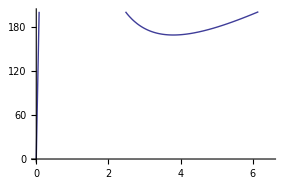

```mathematica
Plot[A[s],{s,0,6.5},PlotRange->{{0,6.5},{0,200}}]
```

## Output tables

The output tables are A in keV vs alpha energy in MeV.   E = 0.09924 s^2 MeV.

```mathematica
tableAEe=Table[{0.09924*s^2,Ae[s]},{s,0,6,0.1}]
```

{{0.,0.},{0.0009924,2.65499},{0.0039696,5.35363},{0.0089316,8.13452},{0.0158784,11.0252},{0.02481,14.0344},{0.0357264,17.145},{0.0486276,20.3119},{0.0635136,23.477},{0.0803844,26.5945},{0.09924,29.6466},{0.12008,32.6378},{0.142906,35.5821},{0.167716,38.4938},{0.19451,41.3843},{0.22329,44.262},{0.254054,47.132},{0.286804,49.9978},{0.321538,52.8614},{0.358256,55.7238},{0.39696,58.5857},{0.437648,61.4472},{0.480322,64.3086},{0.52498,67.1698},{0.571622,70.0307},{0.62025,72.8912},{0.670862,75.7513},{0.72346,78.6107},{0.778042,81.4695},{0.834608,84.3273},{0.89316,87.1841},{0.953696,90.0398},{1.01622,92.8943},{1.08072,95.7474},{1.14721,98.599},{1.21569,101.449},{1.28615,104.297},{1.3586,107.144},{1.43303,109.988},{1.50944,112.831},{1.58784,115.672},{1.66822,118.51},{1.75059,121.346},{1.83495,124.18},{1.92129,127.011},{2.00961,129.84},{2.09992,132.666},{2.19221,135.489},{2.28649,138.31},{2.38275,141.128},{2.481,143.943},{2.58123,146.755},{2.68345,149.563},{2.78765,152.369},{2.89384,155.172},{3.00201,157.971},{3.11217,160.767},{3.22431,163.559},{3.33843,166.348},{3.45454,169.134},{3.57264,171.915}}

```mathematica
tableAEI=Table[{0.09924*s^2,AI[s]},{s,0,6,0.1}]
```

{{0.,-2.84217×10^-14},{0.0009924,246.996},{0.0039696,466.918},{0.0089316,638.525},{0.0158784,750.401},{0.02481,802.008},{0.0357264,801.862},{0.0486276,763.857},{0.0635136,703.155},{0.0803844,632.828},{0.09924,562.102},{0.12008,496.293},{0.142906,437.744},{0.167716,386.951},{0.19451,343.44},{0.22329,306.337},{0.254054,274.683},{0.286804,247.584},{0.321538,224.265},{0.358256,204.084},{0.39696,186.514},{0.437648,171.129},{0.480322,157.583},{0.52498,145.594},{0.571622,134.934},{0.62025,125.411},{0.670862,116.87},{0.72346,109.179},{0.778042,102.229},{0.834608,95.9267},{0.89316,90.1945},{0.953696,84.9652},{1.01622,80.1813},{1.08072,75.7935},{1.14721,71.759},{1.21569,68.0408},{1.28615,64.6066},{1.3586,61.428},{1.43303,58.4803},{1.50944,55.7414},{1.58784,53.1921},{1.66822,50.8153},{1.75059,48.5955},{1.83495,46.5194},{1.92129,44.5746},{2.00961,42.7504},{2.09992,41.0369},{2.19221,39.4253},{2.28649,37.9076},{2.38275,36.4768},{2.481,35.1261},{2.58123,33.8499},{2.68345,32.6426},{2.78765,31.4993},{2.89384,30.4157},{3.00201,29.3876},{3.11217,28.4113},{3.22431,27.4833},{3.33843,26.6005},{3.45454,25.76},{3.57264,24.9591}}

```mathematica
tableAE=Table[{0.09924*s^2,A[s]},{s,0,6,0.1}]
```

{{0.,-2.84217×10^-14},{0.0009924,249.651},{0.0039696,472.272},{0.0089316,646.659},{0.0158784,761.426},{0.02481,816.043},{0.0357264,819.007},{0.0486276,784.169},{0.0635136,726.632},{0.0803844,659.422},{0.09924,591.748},{0.12008,528.931},{0.142906,473.326},{0.167716,425.445},{0.19451,384.824},{0.22329,350.599},{0.254054,321.815},{0.286804,297.581},{0.321538,277.126},{0.358256,259.808},{0.39696,245.099},{0.437648,232.576},{0.480322,221.891},{0.52498,212.764},{0.571622,204.964},{0.62025,198.302},{0.670862,192.621},{0.72346,187.789},{0.778042,183.698},{0.834608,180.254},{0.89316,177.379},{0.953696,175.005},{1.01622,173.076},{1.08072,171.541},{1.14721,170.358},{1.21569,169.49},{1.28615,168.904},{1.3586,168.572},{1.43303,168.469},{1.50944,168.572},{1.58784,168.864},{1.66822,169.325},{1.75059,169.942},{1.83495,170.699},{1.92129,171.586},{2.00961,172.59},{2.09992,173.703},{2.19221,174.915},{2.28649,176.218},{2.38275,177.605},{2.481,179.069},{2.58123,180.604},{2.68345,182.206},{2.78765,183.869},{2.89384,185.587},{3.00201,187.358},{3.11217,189.178},{3.22431,191.042},{3.33843,192.949},{3.45454,194.893},{3.57264,196.874}}

```mathematica
tableAll=Table[{k,3.5*k,0.00025*A[0.098*Sqrt[3.5*k]],0.00025*Ae[0.098*Sqrt[3.5*k]],0.00025*AI[0.098*Sqrt[3.5*k]]},{k,0,1000}]
```

{{0,0.,-7.10543×10^-18,0.,-7.10543×10^-18},{1,3.5,0.10949,0.00122485,0.108266},{2,7.,0.145551,0.00174764,0.143804},{3,10.5,0.167784,0.00215845,0.165626},{4,14.,0.182461,0.00251233,0.179949},{5,17.5,0.192356,0.00282999,0.189526},{6,21.,0.198807,0.00312219,0.195685},{7,24.5,0.202844,0.00339461,0.19945},{8,28.,0.205021,0.00365141,0.20137},{9,31.5,0.205779,0.00389514,0.201884},{10,35.,0.205476,0.00412747,0.201349},{11,38.5,0.204349,0.00434984,0.199999},{12,42.,0.202576,0.00456338,0.198013},{13,45.5,0.200318,0.00476882,0.195549},{14,49.,0.19769,0.00496683,0.192723},{15,52.5,0.194796,0.00515793,0.189638},{16,56.,0.191713,0.0053426,0.18637},{17,59.5,0.188487,0.00552136,0.182966},{18,63.,0.185167,0.00569461,0.179472},{19,66.5,0.181792,0.00586268,0.17593},{20,70.,0.178429,0.00602564,0.172404},{21,73.5,0.175069,0.00618404,0.168885},{22,77.,0.171728,0.00633816,0.16539},{23,80.5,0.168424,0.00648827,0.161935},{24,84.,0.165168,0.0066346,0.158534},{25,87.5,0.162001,0.00677719,0.155224},{26,91.,0.158903,0.0069164,0.151987},{27,94.5,0.155875,0.00705245,0.148822},{28,98.,0.15292,0.00718552,0.145735},{29,101.5,0.150042,0.00731577,0.142727},{30,105.,0.147249,0.00744334,0.139805},{31,108.5,0.144551,0.00756833,0.136983},{32,112.,0.141932,0.00769093,0.134241},{33,115.5,0.139391,0.00781126,0.13158},{34,119.,0.136927,0.00792945,0.128998},{35,122.5,0.134539,0.0080456,0.126494},{36,126.,0.132226,0.00815981,0.124066},{37,129.5,0.129997,0.00827216,0.121725},{38,133.,0.12784,0.00838276,0.119457},{39,136.5,0.125751,0.00849167,0.11726},{40,140.,0.123729,0.00859898,0.11513},{41,143.5,0.121771,0.00870476,0.113066},{42,147.,0.119876,0.00880907,0.111067},{43,150.5,0.118042,0.00891197,0.10913},{44,154.,0.116271,0.00901355,0.107257},{45,157.5,0.114557,0.00911383,0.105443},{46,161.,0.112896,0.00921286,0.103683},{47,164.5,0.111288,0.0093107,0.101978},{48,168.,0.10973,0.00940739,0.100323},{49,171.5,0.108221,0.00950297,0.0987178},{50,175.,0.106758,0.00959748,0.0971604},{51,178.5,0.105342,0.00969097,0.0956505},{52,182.,0.103969,0.00978347,0.0941855},{53,185.5,0.102638,0.00987501,0.092763},{54,189.,0.101347,0.00996562,0.0913814},{55,192.5,0.100095,0.0100553,0.0900392},{56,196.,0.0988789,0.0101442,0.0887348},{57,199.5,0.097699,0.0102321,0.0874668},{58,203.,0.0965533,0.0103193,0.086234},{59,206.5,0.0954409,0.0104057,0.0850352},{60,210.,0.0943605,0.0104913,0.0838692},{61,213.5,0.0933106,0.0105762,0.0827345},{62,217.,0.0922903,0.0106603,0.08163},{63,220.5,0.0912983,0.0107437,0.0805546},{64,224.,0.0903336,0.0108264,0.0795072},{65,227.5,0.0893953,0.0109085,0.0784868},{66,231.,0.0884823,0.0109899,0.0774925},{67,234.5,0.0875939,0.0110706,0.0765233},{68,238.,0.0867287,0.0111507,0.0755779},{69,241.5,0.0858863,0.0112303,0.074656},{70,245.,0.0850658,0.0113092,0.0737566},{71,248.5,0.0842666,0.0113876,0.0728791},{72,252.,0.0834879,0.0114653,0.0720225},{73,255.5,0.0827289,0.0115426,0.0711863},{74,259.,0.081989,0.0116193,0.0703697},{75,262.5,0.0812675,0.0116954,0.0695721},{76,266.,0.0805639,0.011771,0.0687928},{77,269.5,0.079877,0.0118462,0.0680308},{78,273.,0.0792066,0.0119208,0.0672858},{79,276.5,0.0785524,0.011995,0.0665574},{80,280.,0.0779137,0.0120686,0.0658451},{81,283.5,0.0772901,0.0121418,0.0651483},{82,287.,0.0766812,0.0122146,0.0644666},{83,290.5,0.0760863,0.0122869,0.0637994},{84,294.,0.0755052,0.0123587,0.0631465},{85,297.5,0.0749373,0.0124302,0.0625071},{86,301.,0.0743822,0.0125012,0.0618811},{87,304.5,0.073839,0.0125717,0.0612673},{88,308.,0.0733079,0.0126419,0.060666},{89,311.5,0.0727885,0.0127117,0.0600768},{90,315.,0.0722805,0.0127811,0.0594994},{91,318.5,0.0717834,0.01285,0.0589334},{92,322.,0.0712971,0.0129186,0.0583784},{93,325.5,0.0708211,0.0129869,0.0578343},{94,329.,0.0703553,0.0130547,0.0573005},{95,332.5,0.0698992,0.0131222,0.0567769},{96,336.,0.0694526,0.0131894,0.0562632},{97,339.5,0.0690149,0.0132562,0.0557588},{98,343.,0.0685861,0.0133226,0.0552635},{99,346.5,0.0681659,0.0133887,0.0547772},{100,350.,0.0677542,0.0134545,0.0542998},{101,353.5,0.0673508,0.0135199,0.0538309},{102,357.,0.0669555,0.013585,0.0533704},{103,360.5,0.0665679,0.0136498,0.0529181},{104,364.,0.066188,0.0137143,0.0524737},{105,367.5,0.0658154,0.0137785,0.052037},{106,371.,0.0654501,0.0138423,0.0516078},{107,374.5,0.0650918,0.0139059,0.0511859},{108,378.,0.0647401,0.0139691,0.0507709},{109,381.5,0.0643949,0.0140321,0.0503627},{110,385.,0.0640561,0.0140948,0.0499613},{111,388.5,0.0637237,0.0141572,0.0495665},{112,392.,0.0633975,0.0142193,0.0491782},{113,395.5,0.0630773,0.0142811,0.0487961},{114,399.,0.0627629,0.0143427,0.0484202},{115,402.5,0.0624543,0.014404,0.0480503},{116,406.,0.0621513,0.014465,0.0476862},{117,409.5,0.0618537,0.0145258,0.0473279},{118,413.,0.0615614,0.0145863,0.0469751},{119,416.5,0.0612743,0.0146465,0.0466278},{120,420.,0.060992,0.0147065,0.0462854},{121,423.5,0.0607146,0.0147663,0.0459483},{122,427.,0.060442,0.0148258,0.0456163},{123,430.5,0.0601742,0.014885,0.0452892},{124,434.,0.059911,0.014944,0.0449669},{125,437.5,0.0596523,0.0150028,0.0446494},{126,441.,0.059398,0.0150613,0.0443366},{127,444.5,0.059148,0.0151197,0.0440283},{128,448.,0.0589022,0.0151777,0.0437244},{129,451.5,0.0586605,0.0152356,0.0434249},{130,455.,0.0584229,0.0152932,0.0431297},{131,458.5,0.0581892,0.0153506,0.0428385},{132,462.,0.0579591,0.0154078,0.0425513},{133,465.5,0.0577328,0.0154648,0.042268},{134,469.,0.0575102,0.0155215,0.0419886},{135,472.5,0.0572911,0.0155781,0.0417131},{136,476.,0.0570757,0.0156344,0.0414412},{137,479.5,0.0568636,0.0156905,0.0411731},{138,483.,0.056655,0.0157465,0.0409085},{139,486.5,0.0564497,0.0158022,0.0406475},{140,490.,0.0562476,0.0158577,0.0403899},{141,493.5,0.0560487,0.015913,0.0401357},{142,497.,0.0558529,0.0159682,0.0398848},{143,500.5,0.0556602,0.0160231,0.0396371},{144,504.,0.0554705,0.0160778,0.0393926},{145,507.5,0.0552835,0.0161324,0.0391511},{146,511.,0.0550994,0.0161867,0.0389127},{147,514.5,0.0549181,0.0162409,0.0386772},{148,518.,0.0547396,0.0162949,0.0384447},{149,521.5,0.0545638,0.0163487,0.0382151},{150,525.,0.0543906,0.0164023,0.0379883},{151,528.5,0.0542201,0.0164558,0.0377643},{152,532.,0.0540521,0.0165091,0.0375431},{153,535.5,0.0538866,0.0165622,0.0373245},{154,539.,0.0537236,0.0166151,0.0371085},{155,542.5,0.053563,0.0166678,0.0368952},{156,546.,0.0534048,0.0167204,0.0366844},{157,549.5,0.0532489,0.0167728,0.036476},{158,553.,0.0530952,0.0168251,0.0362701},{159,556.5,0.0529437,0.0168772,0.0360665},{160,560.,0.0527943,0.0169291,0.0358653},{161,563.5,0.0526472,0.0169808,0.0356663},{162,567.,0.0525021,0.0170324,0.0354697},{163,570.5,0.0523592,0.0170839,0.0352753},{164,574.,0.0522182,0.0171351,0.0350831},{165,577.5,0.0520793,0.0171863,0.0348931},{166,581.,0.0519424,0.0172372,0.0347052},{167,584.5,0.0518074,0.017288,0.0345194},{168,588.,0.0516743,0.0173387,0.0343356},{169,591.5,0.0515431,0.0173892,0.0341539},{170,595.,0.0514138,0.0174396,0.0339742},{171,598.5,0.0512862,0.0174898,0.0337964},{172,602.,0.0511603,0.0175398,0.0336205},{173,605.5,0.0510362,0.0175898,0.0334465},{174,609.,0.0509138,0.0176395,0.0332743},{175,612.5,0.050793,0.0176892,0.0331039},{176,616.,0.050674,0.0177386,0.0329353},{177,619.5,0.0505565,0.017788,0.0327685},{178,623.,0.0504407,0.0178372,0.0326035},{179,626.5,0.0503264,0.0178863,0.0324402},{180,630.,0.0502137,0.0179352,0.0322785},{181,633.5,0.0501026,0.017984,0.0321186},{182,637.,0.0499929,0.0180326,0.0319602},{183,640.5,0.0498847,0.0180812,0.0318035},{184,644.,0.049778,0.0181296,0.0316484},{185,647.5,0.0496727,0.0181778,0.0314948},{186,651.,0.0495688,0.018226,0.0313428},{187,654.5,0.0494662,0.018274,0.0311922},{188,658.,0.049365,0.0183218,0.0310432},{189,661.5,0.0492651,0.0183696,0.0308955},{190,665.,0.0491666,0.0184172,0.0307494},{191,668.5,0.0490693,0.0184647,0.0306046},{192,672.,0.0489733,0.018512,0.0304613},{193,675.5,0.0488786,0.0185593,0.0303193},{194,679.,0.0487852,0.0186064,0.0301788},{195,682.5,0.048693,0.0186534,0.0300395},{196,686.,0.0486019,0.0187003,0.0299016},{197,689.5,0.0485121,0.018747,0.029765},{198,693.,0.0484234,0.0187937,0.0296297},{199,696.5,0.0483359,0.0188402,0.0294957},{200,700.,0.0482495,0.0188866,0.0293629},{201,703.5,0.0481643,0.0189329,0.0292314},{202,707.,0.04808,0.0189791,0.029101},{203,710.5,0.0479969,0.0190251,0.0289718},{204,714.,0.0479148,0.0190711,0.0288438},{205,717.5,0.0478338,0.0191169,0.0287169},{206,721.,0.0477539,0.0191626,0.0285913},{207,724.5,0.0476749,0.0192082,0.0284667},{208,728.,0.047597,0.0192537,0.0283433},{209,731.5,0.04752,0.0192991,0.0282209},{210,735.,0.0474441,0.0193444,0.0280997},{211,738.5,0.0473691,0.0193895,0.0279795},{212,742.,0.047295,0.0194346,0.0278604},{213,745.5,0.0472219,0.0194795,0.0277424},{214,749.,0.0471498,0.0195244,0.0276254},{215,752.5,0.0470785,0.0195691,0.0275094},{216,756.,0.0470081,0.0196138,0.0273944},{217,759.5,0.0469387,0.0196583,0.0272804},{218,763.,0.04687,0.0197027,0.0271673},{219,766.5,0.0468022,0.019747,0.0270552},{220,770.,0.0467353,0.0197913,0.026944},{221,773.5,0.0466692,0.0198354,0.0268338},{222,777.,0.046604,0.0198794,0.0267245},{223,780.5,0.0465395,0.0199233,0.0266162},{224,784.,0.0464759,0.0199672,0.0265087},{225,787.5,0.0464131,0.0200109,0.0264022},{226,791.,0.046351,0.0200545,0.0262965},{227,794.5,0.0462897,0.0200981,0.0261917},{228,798.,0.0462292,0.0201415,0.0260877},{229,801.5,0.0461695,0.0201848,0.0259847},{230,805.,0.0461105,0.0202281,0.0258824},{231,808.5,0.0460522,0.0202712,0.025781},{232,812.,0.0459947,0.0203143,0.0256804},{233,815.5,0.0459378,0.0203572,0.0255806},{234,819.,0.0458817,0.0204001,0.0254816},{235,822.5,0.0458262,0.0204429,0.0253833},{236,826.,0.0457714,0.0204856,0.0252859},{237,829.5,0.0457174,0.0205282,0.0251892},{238,833.,0.0456639,0.0205707,0.0250933},{239,836.5,0.0456112,0.0206131,0.0249981},{240,840.,0.0455591,0.0206554,0.0249037},{241,843.5,0.0455076,0.0206976,0.02481},{242,847.,0.0454568,0.0207398,0.024717},{243,850.5,0.0454066,0.0207818,0.0246248},{244,854.,0.0453571,0.0208238,0.0245333},{245,857.5,0.0453081,0.0208657,0.0244424},{246,861.,0.0452598,0.0209075,0.0243523},{247,864.5,0.045212,0.0209492,0.0242628},{248,868.,0.0451649,0.0209908,0.0241741},{249,871.5,0.0451183,0.0210324,0.024086},{250,875.,0.0450723,0.0210738,0.0239985},{251,878.5,0.0450269,0.0211152,0.0239117},{252,882.,0.044982,0.0211565,0.0238255},{253,885.5,0.0449377,0.0211977,0.02374},{254,889.,0.0448939,0.0212388,0.0236551},{255,892.5,0.0448507,0.0212799,0.0235708},{256,896.,0.044808,0.0213208,0.0234872},{257,899.5,0.0447658,0.0213617,0.0234041},{258,903.,0.0447242,0.0214025,0.0233217},{259,906.5,0.0446831,0.0214432,0.0232398},{260,910.,0.0446425,0.0214839,0.0231586},{261,913.5,0.0446024,0.0215244,0.0230779},{262,917.,0.0445628,0.0215649,0.0229978},{263,920.5,0.0445237,0.0216053,0.0229183},{264,924.,0.044485,0.0216457,0.0228394},{265,927.5,0.0444469,0.0216859,0.022761},{266,931.,0.0444093,0.0217261,0.0226832},{267,934.5,0.0443721,0.0217662,0.0226059},{268,938.,0.0443354,0.0218062,0.0225292},{269,941.5,0.0442991,0.0218462,0.0224529},{270,945.,0.0442633,0.021886,0.0223772},{271,948.5,0.0442279,0.0219258,0.0223021},{272,952.,0.044193,0.0219655,0.0222274},{273,955.5,0.0441585,0.0220052,0.0221533},{274,959.,0.0441244,0.0220448,0.0220797},{275,962.5,0.0440908,0.0220843,0.0220065},{276,966.,0.0440576,0.0221237,0.0219339},{277,969.5,0.0440249,0.0221631,0.0218618},{278,973.,0.0439925,0.0222024,0.0217901},{279,976.5,0.0439606,0.0222416,0.021719},{280,980.,0.043929,0.0222807,0.0216483},{281,983.5,0.0438979,0.0223198,0.0215781},{282,987.,0.0438672,0.0223588,0.0215084},{283,990.5,0.0438368,0.0223977,0.0214391},{284,994.,0.0438069,0.0224366,0.0213703},{285,997.5,0.0437773,0.0224754,0.0213019},{286,1001.,0.0437481,0.0225141,0.021234},{287,1004.5,0.0437193,0.0225528,0.0211666},{288,1008.,0.0436909,0.0225914,0.0210995},{289,1011.5,0.0436628,0.0226299,0.0210329},{290,1015.,0.0436351,0.0226683,0.0209668},{291,1018.5,0.0436077,0.0227067,0.020901},{292,1022.,0.0435807,0.022745,0.0208357},{293,1025.5,0.0435541,0.0227833,0.0207708},{294,1029.,0.0435278,0.0228215,0.0207063},{295,1032.5,0.0435018,0.0228596,0.0206423},{296,1036.,0.0434762,0.0228976,0.0205786},{297,1039.5,0.043451,0.0229356,0.0205153},{298,1043.,0.043426,0.0229736,0.0204525},{299,1046.5,0.0434015,0.0230114,0.02039},{300,1050.,0.0433772,0.0230492,0.020328},{301,1053.5,0.0433532,0.0230869,0.0202663},{302,1057.,0.0433296,0.0231246,0.020205},{303,1060.5,0.0433063,0.0231622,0.0201441},{304,1064.,0.0432833,0.0231998,0.0200836},{305,1067.5,0.0432606,0.0232372,0.0200234},{306,1071.,0.0432383,0.0232747,0.0199636},{307,1074.5,0.0432162,0.023312,0.0199042},{308,1078.,0.0431944,0.0233493,0.0198451},{309,1081.5,0.0431729,0.0233865,0.0197864},{310,1085.,0.0431518,0.0234237,0.019728},{311,1088.5,0.0431309,0.0234608,0.01967},{312,1092.,0.0431103,0.0234979,0.0196124},{313,1095.5,0.04309,0.0235349,0.0195551},{314,1099.,0.0430699,0.0235718,0.0194981},{315,1102.5,0.0430502,0.0236087,0.0194415},{316,1106.,0.0430307,0.0236455,0.0193853},{317,1109.5,0.0430115,0.0236822,0.0193293},{318,1113.,0.0429926,0.0237189,0.0192737},{319,1116.5,0.042974,0.0237556,0.0192184},{320,1120.,0.0429556,0.0237921,0.0191635},{321,1123.5,0.0429375,0.0238286,0.0191089},{322,1127.,0.0429196,0.0238651,0.0190545},{323,1130.5,0.0429021,0.0239015,0.0190006},{324,1134.,0.0428847,0.0239379,0.0189469},{325,1137.5,0.0428676,0.0239741,0.0188935},{326,1141.,0.0428508,0.0240104,0.0188404},{327,1144.5,0.0428342,0.0240465,0.0187877},{328,1148.,0.0428179,0.0240827,0.0187352},{329,1151.5,0.0428018,0.0241187,0.0186831},{330,1155.,0.0427859,0.0241547,0.0186312},{331,1158.5,0.0427703,0.0241907,0.0185796},{332,1162.,0.042755,0.0242266,0.0185284},{333,1165.5,0.0427398,0.0242624,0.0184774},{334,1169.,0.0427249,0.0242982,0.0184267},{335,1172.5,0.0427103,0.0243339,0.0183763},{336,1176.,0.0426958,0.0243696,0.0183262},{337,1179.5,0.0426816,0.0244052,0.0182764},{338,1183.,0.0426676,0.0244408,0.0182268},{339,1186.5,0.0426538,0.0244763,0.0181775},{340,1190.,0.0426403,0.0245118,0.0181285},{341,1193.5,0.042627,0.0245472,0.0180798},{342,1197.,0.0426139,0.0245826,0.0180313},{343,1200.5,0.042601,0.0246179,0.0179831},{344,1204.,0.0425883,0.0246531,0.0179352},{345,1207.5,0.0425758,0.0246883,0.0178875},{346,1211.,0.0425635,0.0247235,0.0178401},{347,1214.5,0.0425515,0.0247586,0.0177929},{348,1218.,0.0425396,0.0247936,0.017746},{349,1221.5,0.0425279,0.0248286,0.0176994},{350,1225.,0.0425165,0.0248635,0.017653},{351,1228.5,0.0425052,0.0248984,0.0176068},{352,1232.,0.0424942,0.0249333,0.0175609},{353,1235.5,0.0424833,0.0249681,0.0175152},{354,1239.,0.0424726,0.0250028,0.0174698},{355,1242.5,0.0424622,0.0250375,0.0174247},{356,1246.,0.0424519,0.0250721,0.0173797},{357,1249.5,0.0424418,0.0251067,0.017335},{358,1253.,0.0424319,0.0251413,0.0172906},{359,1256.5,0.0424221,0.0251758,0.0172464},{360,1260.,0.0424126,0.0252102,0.0172024},{361,1263.5,0.0424032,0.0252446,0.0171586},{362,1267.,0.042394,0.0252789,0.0171151},{363,1270.5,0.042385,0.0253132,0.0170718},{364,1274.,0.0423762,0.0253475,0.0170287},{365,1277.5,0.0423676,0.0253817,0.0169859},{366,1281.,0.0423591,0.0254158,0.0169432},{367,1284.5,0.0423508,0.0254499,0.0169008},{368,1288.,0.0423426,0.025484,0.0168586},{369,1291.5,0.0423346,0.025518,0.0168166},{370,1295.,0.0423268,0.025552,0.0167749},{371,1298.5,0.0423192,0.0255859,0.0167333},{372,1302.,0.0423117,0.0256198,0.016692},{373,1305.5,0.0423044,0.0256536,0.0166508},{374,1309.,0.0422973,0.0256874,0.0166099},{375,1312.5,0.0422903,0.0257211,0.0165692},{376,1316.,0.0422834,0.0257548,0.0165287},{377,1319.5,0.0422768,0.0257884,0.0164883},{378,1323.,0.0422703,0.025822,0.0164482},{379,1326.5,0.0422639,0.0258556,0.0164083},{380,1330.,0.0422577,0.0258891,0.0163686},{381,1333.5,0.0422516,0.0259225,0.0163291},{382,1337.,0.0422457,0.0259559,0.0162898},{383,1340.5,0.04224,0.0259893,0.0162507},{384,1344.,0.0422344,0.0260226,0.0162117},{385,1347.5,0.0422289,0.0260559,0.016173},{386,1351.,0.0422236,0.0260892,0.0161345},{387,1354.5,0.0422184,0.0261223,0.0160961},{388,1358.,0.0422134,0.0261555,0.0160579},{389,1361.5,0.0422085,0.0261886,0.0160199},{390,1365.,0.0422038,0.0262217,0.0159821},{391,1368.5,0.0421992,0.0262547,0.0159445},{392,1372.,0.0421947,0.0262877,0.0159071},{393,1375.5,0.0421904,0.0263206,0.0158698},{394,1379.,0.0421862,0.0263535,0.0158327},{395,1382.5,0.0421821,0.0263863,0.0157958},{396,1386.,0.0421782,0.0264191,0.0157591},{397,1389.5,0.0421744,0.0264519,0.0157225},{398,1393.,0.0421708,0.0264846,0.0156862},{399,1396.5,0.0421672,0.0265173,0.01565},{400,1400.,0.0421638,0.0265499,0.0156139},{401,1403.5,0.0421606,0.0265825,0.0155781},{402,1407.,0.0421574,0.0266151,0.0155424},{403,1410.5,0.0421544,0.0266476,0.0155069},{404,1414.,0.0421515,0.02668,0.0154715},{405,1417.5,0.0421488,0.0267125,0.0154363},{406,1421.,0.0421461,0.0267449,0.0154013},{407,1424.5,0.0421436,0.0267772,0.0153664},{408,1428.,0.0421412,0.0268095,0.0153317},{409,1431.5,0.0421389,0.0268418,0.0152972},{410,1435.,0.0421368,0.026874,0.0152628},{411,1438.5,0.0421347,0.0269062,0.0152286},{412,1442.,0.0421328,0.0269383,0.0151945},{413,1445.5,0.042131,0.0269704,0.0151606},{414,1449.,0.0421293,0.0270025,0.0151268},{415,1452.5,0.0421277,0.0270345,0.0150932},{416,1456.,0.0421263,0.0270665,0.0150598},{417,1459.5,0.0421249,0.0270984,0.0150265},{418,1463.,0.0421237,0.0271304,0.0149933},{419,1466.5,0.0421225,0.0271622,0.0149603},{420,1470.,0.0421215,0.027194,0.0149275},{421,1473.5,0.0421206,0.0272258,0.0148948},{422,1477.,0.0421198,0.0272576,0.0148622},{423,1480.5,0.0421191,0.0272893,0.0148298},{424,1484.,0.0421185,0.027321,0.0147975},{425,1487.5,0.042118,0.0273526,0.0147654},{426,1491.,0.0421177,0.0273842,0.0147335},{427,1494.5,0.0421174,0.0274158,0.0147016},{428,1498.,0.0421172,0.0274473,0.0146699},{429,1501.5,0.0421172,0.0274788,0.0146384},{430,1505.,0.0421172,0.0275102,0.014607},{431,1508.5,0.0421173,0.0275416,0.0145757},{432,1512.,0.0421176,0.027573,0.0145446},{433,1515.5,0.0421179,0.0276043,0.0145136},{434,1519.,0.0421183,0.0276356,0.0144827},{435,1522.5,0.0421188,0.0276669,0.014452},{436,1526.,0.0421195,0.0276981,0.0144214},{437,1529.5,0.0421202,0.0277293,0.0143909},{438,1533.,0.042121,0.0277604,0.0143606},{439,1536.5,0.0421219,0.0277916,0.0143304},{440,1540.,0.0421229,0.0278226,0.0143003},{441,1543.5,0.042124,0.0278537,0.0142703},{442,1547.,0.0421252,0.0278847,0.0142405},{443,1550.5,0.0421265,0.0279156,0.0142108},{444,1554.,0.0421279,0.0279466,0.0141813},{445,1557.5,0.0421293,0.0279775,0.0141519},{446,1561.,0.0421309,0.0280083,0.0141226},{447,1564.5,0.0421325,0.0280392,0.0140934},{448,1568.,0.0421343,0.0280699,0.0140643},{449,1571.5,0.0421361,0.0281007,0.0140354},{450,1575.,0.042138,0.0281314,0.0140066},{451,1578.5,0.04214,0.0281621,0.0139779},{452,1582.,0.0421421,0.0281928,0.0139493},{453,1585.5,0.0421442,0.0282234,0.0139209},{454,1589.,0.0421465,0.0282539,0.0138925},{455,1592.5,0.0421488,0.0282845,0.0138643},{456,1596.,0.0421512,0.028315,0.0138362},{457,1599.5,0.0421537,0.0283455,0.0138082},{458,1603.,0.0421563,0.0283759,0.0137804},{459,1606.5,0.0421589,0.0284063,0.0137526},{460,1610.,0.0421617,0.0284367,0.013725},{461,1613.5,0.0421645,0.028467,0.0136974},{462,1617.,0.0421674,0.0284973,0.01367},{463,1620.5,0.0421704,0.0285276,0.0136427},{464,1624.,0.0421734,0.0285579,0.0136156},{465,1627.5,0.0421765,0.0285881,0.0135885},{466,1631.,0.0421797,0.0286182,0.0135615},{467,1634.5,0.042183,0.0286484,0.0135347},{468,1638.,0.0421864,0.0286785,0.0135079},{469,1641.5,0.0421898,0.0287085,0.0134813},{470,1645.,0.0421933,0.0287386,0.0134548},{471,1648.5,0.0421969,0.0287686,0.0134283},{472,1652.,0.0422006,0.0287986,0.013402},{473,1655.5,0.0422043,0.0288285,0.0133758},{474,1659.,0.0422081,0.0288584,0.0133497},{475,1662.5,0.042212,0.0288883,0.0133237},{476,1666.,0.042216,0.0289181,0.0132978},{477,1669.5,0.04222,0.0289479,0.013272},{478,1673.,0.0422241,0.0289777,0.0132463},{479,1676.5,0.0422282,0.0290075,0.0132208},{480,1680.,0.0422324,0.0290372,0.0131953},{481,1683.5,0.0422367,0.0290669,0.0131699},{482,1687.,0.0422411,0.0290965,0.0131446},{483,1690.5,0.0422455,0.0291261,0.0131194},{484,1694.,0.04225,0.0291557,0.0130943},{485,1697.5,0.0422546,0.0291853,0.0130693},{486,1701.,0.0422592,0.0292148,0.0130444},{487,1704.5,0.0422639,0.0292443,0.0130196},{488,1708.,0.0422687,0.0292737,0.0129949},{489,1711.5,0.0422735,0.0293032,0.0129703},{490,1715.,0.0422784,0.0293326,0.0129458},{491,1718.5,0.0422834,0.0293619,0.0129214},{492,1722.,0.0422884,0.0293913,0.0128971},{493,1725.5,0.0422935,0.0294206,0.0128729},{494,1729.,0.0422986,0.0294499,0.0128488},{495,1732.5,0.0423038,0.0294791,0.0128247},{496,1736.,0.0423091,0.0295083,0.0128008},{497,1739.5,0.0423144,0.0295375,0.0127769},{498,1743.,0.0423198,0.0295667,0.0127532},{499,1746.5,0.0423253,0.0295958,0.0127295},{500,1750.,0.0423308,0.0296249,0.0127059},{501,1753.5,0.0423364,0.0296539,0.0126824},{502,1757.,0.042342,0.029683,0.012659},{503,1760.5,0.0423477,0.029712,0.0126357},{504,1764.,0.0423534,0.029741,0.0126125},{505,1767.5,0.0423592,0.0297699,0.0125893},{506,1771.,0.0423651,0.0297988,0.0125663},{507,1774.5,0.042371,0.0298277,0.0125433},{508,1778.,0.042377,0.0298566,0.0125204},{509,1781.5,0.042383,0.0298854,0.0124976},{510,1785.,0.0423891,0.0299142,0.0124749},{511,1788.5,0.0423953,0.029943,0.0124523},{512,1792.,0.0424015,0.0299717,0.0124298},{513,1795.5,0.0424077,0.0300004,0.0124073},{514,1799.,0.042414,0.0300291,0.0123849},{515,1802.5,0.0424204,0.0300577,0.0123626},{516,1806.,0.0424268,0.0300864,0.0123404},{517,1809.5,0.0424333,0.030115,0.0123183},{518,1813.,0.0424398,0.0301435,0.0122963},{519,1816.5,0.0424464,0.0301721,0.0122743},{520,1820.,0.042453,0.0302006,0.0122524},{521,1823.5,0.0424597,0.030229,0.0122306},{522,1827.,0.0424664,0.0302575,0.0122089},{523,1830.5,0.0424732,0.0302859,0.0121872},{524,1834.,0.04248,0.0303143,0.0121657},{525,1837.5,0.0424869,0.0303427,0.0121442},{526,1841.,0.0424938,0.030371,0.0121228},{527,1844.5,0.0425008,0.0303993,0.0121014},{528,1848.,0.0425078,0.0304276,0.0120802},{529,1851.5,0.0425149,0.0304559,0.012059},{530,1855.,0.042522,0.0304841,0.0120379},{531,1858.5,0.0425292,0.0305123,0.0120169},{532,1862.,0.0425364,0.0305405,0.0119959},{533,1865.5,0.0425437,0.0305686,0.011975},{534,1869.,0.042551,0.0305968,0.0119542},{535,1872.5,0.0425584,0.0306249,0.0119335},{536,1876.,0.0425658,0.0306529,0.0119129},{537,1879.5,0.0425732,0.030681,0.0118923},{538,1883.,0.0425807,0.030709,0.0118718},{539,1886.5,0.0425883,0.030737,0.0118513},{540,1890.,0.0425959,0.0307649,0.011831},{541,1893.5,0.0426035,0.0307928,0.0118107},{542,1897.,0.0426112,0.0308207,0.0117904},{543,1900.5,0.0426189,0.0308486,0.0117703},{544,1904.,0.0426267,0.0308765,0.0117502},{545,1907.5,0.0426345,0.0309043,0.0117302},{546,1911.,0.0426424,0.0309321,0.0117103},{547,1914.5,0.0426503,0.0309599,0.0116904},{548,1918.,0.0426582,0.0309876,0.0116706},{549,1921.5,0.0426662,0.0310153,0.0116509},{550,1925.,0.0426742,0.031043,0.0116312},{551,1928.5,0.0426823,0.0310707,0.0116116},{552,1932.,0.0426904,0.0310983,0.0115921},{553,1935.5,0.0426985,0.0311259,0.0115726},{554,1939.,0.0427067,0.0311535,0.0115532},{555,1942.5,0.042715,0.0311811,0.0115339},{556,1946.,0.0427232,0.0312086,0.0115146},{557,1949.5,0.0427316,0.0312361,0.0114954},{558,1953.,0.0427399,0.0312636,0.0114763},{559,1956.5,0.0427483,0.0312911,0.0114572},{560,1960.,0.0427567,0.0313185,0.0114382},{561,1963.5,0.0427652,0.0313459,0.0114193},{562,1967.,0.0427737,0.0313733,0.0114004},{563,1970.5,0.0427823,0.0314007,0.0113816},{564,1974.,0.0427909,0.031428,0.0113629},{565,1977.5,0.0427995,0.0314553,0.0113442},{566,1981.,0.0428082,0.0314826,0.0113256},{567,1984.5,0.0428169,0.0315099,0.011307},{568,1988.,0.0428256,0.0315371,0.0112885},{569,1991.5,0.0428344,0.0315643,0.0112701},{570,1995.,0.0428432,0.0315915,0.0112517},{571,1998.5,0.042852,0.0316186,0.0112334},{572,2002.,0.0428609,0.0316458,0.0112152},{573,2005.5,0.0428699,0.0316729,0.011197},{574,2009.,0.0428788,0.0317,0.0111788},{575,2012.5,0.0428878,0.031727,0.0111608},{576,2016.,0.0428968,0.0317541,0.0111428},{577,2019.5,0.0429059,0.0317811,0.0111248},{578,2023.,0.042915,0.0318081,0.0111069},{579,2026.5,0.0429241,0.031835,0.0110891},{580,2030.,0.0429333,0.031862,0.0110713},{581,2033.5,0.0429425,0.0318889,0.0110536},{582,2037.,0.0429517,0.0319158,0.011036},{583,2040.5,0.042961,0.0319426,0.0110184},{584,2044.,0.0429703,0.0319695,0.0110008},{585,2047.5,0.0429797,0.0319963,0.0109834},{586,2051.,0.042989,0.0320231,0.0109659},{587,2054.5,0.0429984,0.0320499,0.0109486},{588,2058.,0.0430079,0.0320766,0.0109312},{589,2061.5,0.0430173,0.0321033,0.010914},{590,2065.,0.0430268,0.03213,0.0108968},{591,2068.5,0.0430364,0.0321567,0.0108796},{592,2072.,0.0430459,0.0321834,0.0108626},{593,2075.5,0.0430555,0.03221,0.0108455},{594,2079.,0.0430652,0.0322366,0.0108285},{595,2082.5,0.0430748,0.0322632,0.0108116},{596,2086.,0.0430845,0.0322898,0.0107948},{597,2089.5,0.0430942,0.0323163,0.0107779},{598,2093.,0.043104,0.0323428,0.0107612},{599,2096.5,0.0431138,0.0323693,0.0107445},{600,2100.,0.0431236,0.0323958,0.0107278},{601,2103.5,0.0431334,0.0324222,0.0107112},{602,2107.,0.0431433,0.0324486,0.0106947},{603,2110.5,0.0431532,0.032475,0.0106782},{604,2114.,0.0431631,0.0325014,0.0106617},{605,2117.5,0.0431731,0.0325278,0.0106453},{606,2121.,0.0431831,0.0325541,0.010629},{607,2124.5,0.0431931,0.0325804,0.0106127},{608,2128.,0.0432031,0.0326067,0.0105964},{609,2131.5,0.0432132,0.0326329,0.0105803},{610,2135.,0.0432233,0.0326592,0.0105641},{611,2138.5,0.0432334,0.0326854,0.010548},{612,2142.,0.0432436,0.0327116,0.010532},{613,2145.5,0.0432538,0.0327378,0.010516},{614,2149.,0.043264,0.0327639,0.0105001},{615,2152.5,0.0432742,0.0327901,0.0104842},{616,2156.,0.0432845,0.0328162,0.0104683},{617,2159.5,0.0432948,0.0328422,0.0104525},{618,2163.,0.0433051,0.0328683,0.0104368},{619,2166.5,0.0433155,0.0328943,0.0104211},{620,2170.,0.0433258,0.0329204,0.0104055},{621,2173.5,0.0433362,0.0329464,0.0103899},{622,2177.,0.0433467,0.0329723,0.0103743},{623,2180.5,0.0433571,0.0329983,0.0103588},{624,2184.,0.0433676,0.0330242,0.0103434},{625,2187.5,0.0433781,0.0330501,0.010328},{626,2191.,0.0433886,0.033076,0.0103126},{627,2194.5,0.0433992,0.0331019,0.0102973},{628,2198.,0.0434098,0.0331277,0.010282},{629,2201.5,0.0434204,0.0331536,0.0102668},{630,2205.,0.043431,0.0331794,0.0102516},{631,2208.5,0.0434416,0.0332051,0.0102365},{632,2212.,0.0434523,0.0332309,0.0102214},{633,2215.5,0.043463,0.0332566,0.0102064},{634,2219.,0.0434738,0.0332824,0.0101914},{635,2222.5,0.0434845,0.0333081,0.0101764},{636,2226.,0.0434953,0.0333337,0.0101615},{637,2229.5,0.0435061,0.0333594,0.0101467},{638,2233.,0.0435169,0.033385,0.0101319},{639,2236.5,0.0435277,0.0334106,0.0101171},{640,2240.,0.0435386,0.0334362,0.0101024},{641,2243.5,0.0435495,0.0334618,0.0100877},{642,2247.,0.0435604,0.0334873,0.0100731},{643,2250.5,0.0435713,0.0335129,0.0100585},{644,2254.,0.0435823,0.0335384,0.0100439},{645,2257.5,0.0435933,0.0335639,0.0100294},{646,2261.,0.0436043,0.0335893,0.010015},{647,2264.5,0.0436153,0.0336148,0.0100005},{648,2268.,0.0436264,0.0336402,0.00998616},{649,2271.5,0.0436374,0.0336656,0.00997183},{650,2275.,0.0436485,0.033691,0.00995753},{651,2278.5,0.0436596,0.0337164,0.00994328},{652,2282.,0.0436708,0.0337417,0.00992907},{653,2285.5,0.0436819,0.033767,0.00991491},{654,2289.,0.0436931,0.0337923,0.00990078},{655,2292.5,0.0437043,0.0338176,0.0098867},{656,2296.,0.0437155,0.0338429,0.00987265},{657,2299.5,0.0437268,0.0338681,0.00985865},{658,2303.,0.043738,0.0338933,0.00984469},{659,2306.5,0.0437493,0.0339185,0.00983076},{660,2310.,0.0437606,0.0339437,0.00981688},{661,2313.5,0.0437719,0.0339689,0.00980304},{662,2317.,0.0437833,0.033994,0.00978924},{663,2320.5,0.0437946,0.0340191,0.00977547},{664,2324.,0.043806,0.0340442,0.00976175},{665,2327.5,0.0438174,0.0340693,0.00974807},{666,2331.,0.0438288,0.0340944,0.00973442},{667,2334.5,0.0438403,0.0341194,0.00972082},{668,2338.,0.0438517,0.0341445,0.00970725},{669,2341.5,0.0438632,0.0341695,0.00969373},{670,2345.,0.0438747,0.0341944,0.00968024},{671,2348.5,0.0438862,0.0342194,0.00966679},{672,2352.,0.0438977,0.0342444,0.00965338},{673,2355.5,0.0439093,0.0342693,0.00964},{674,2359.,0.0439209,0.0342942,0.00962667},{675,2362.5,0.0439325,0.0343191,0.00961337},{676,2366.,0.0439441,0.0343439,0.00960011},{677,2369.5,0.0439557,0.0343688,0.00958689},{678,2373.,0.0439673,0.0343936,0.0095737},{679,2376.5,0.043979,0.0344184,0.00956055},{680,2380.,0.0439907,0.0344432,0.00954744},{681,2383.5,0.0440024,0.034468,0.00953437},{682,2387.,0.0440141,0.0344928,0.00952133},{683,2390.5,0.0440258,0.0345175,0.00950833},{684,2394.,0.0440376,0.0345422,0.00949537},{685,2397.5,0.0440493,0.0345669,0.00948244},{686,2401.,0.0440611,0.0345916,0.00946955},{687,2404.5,0.0440729,0.0346162,0.00945669},{688,2408.,0.0440847,0.0346409,0.00944387},{689,2411.5,0.0440966,0.0346655,0.00943108},{690,2415.,0.0441084,0.0346901,0.00941833},{691,2418.5,0.0441203,0.0347147,0.00940562},{692,2422.,0.0441322,0.0347392,0.00939294},{693,2425.5,0.0441441,0.0347638,0.00938029},{694,2429.,0.044156,0.0347883,0.00936768},{695,2432.5,0.0441679,0.0348128,0.00935511},{696,2436.,0.0441799,0.0348373,0.00934257},{697,2439.5,0.0441919,0.0348618,0.00933006},{698,2443.,0.0442038,0.0348863,0.00931759},{699,2446.5,0.0442158,0.0349107,0.00930515},{700,2450.,0.0442279,0.0349351,0.00929275},{701,2453.5,0.0442399,0.0349595,0.00928038},{702,2457.,0.0442519,0.0349839,0.00926804},{703,2460.5,0.044264,0.0350082,0.00925574},{704,2464.,0.0442761,0.0350326,0.00924347},{705,2467.5,0.0442882,0.0350569,0.00923124},{706,2471.,0.0443003,0.0350812,0.00921903},{707,2474.5,0.0443124,0.0351055,0.00920686},{708,2478.,0.0443245,0.0351298,0.00919473},{709,2481.5,0.0443367,0.035154,0.00918263},{710,2485.,0.0443488,0.0351783,0.00917055},{711,2488.5,0.044361,0.0352025,0.00915852},{712,2492.,0.0443732,0.0352267,0.00914651},{713,2495.5,0.0443854,0.0352509,0.00913454},{714,2499.,0.0443976,0.035275,0.0091226},{715,2502.5,0.0444099,0.0352992,0.00911068},{716,2506.,0.0444221,0.0353233,0.00909881},{717,2509.5,0.0444344,0.0353474,0.00908696},{718,2513.,0.0444467,0.0353715,0.00907514},{719,2516.5,0.044459,0.0353956,0.00906336},{720,2520.,0.0444713,0.0354197,0.00905161},{721,2523.5,0.0444836,0.0354437,0.00903989},{722,2527.,0.0444959,0.0354677,0.0090282},{723,2530.5,0.0445083,0.0354917,0.00901654},{724,2534.,0.0445206,0.0355157,0.00900491},{725,2537.5,0.044533,0.0355397,0.00899331},{726,2541.,0.0445454,0.0355636,0.00898175},{727,2544.5,0.0445578,0.0355876,0.00897021},{728,2548.,0.0445702,0.0356115,0.0089587},{729,2551.5,0.0445826,0.0356354,0.00894723},{730,2555.,0.0445951,0.0356593,0.00893578},{731,2558.5,0.0446075,0.0356831,0.00892437},{732,2562.,0.04462,0.035707,0.00891298},{733,2565.5,0.0446325,0.0357308,0.00890163},{734,2569.,0.0446449,0.0357546,0.0088903},{735,2572.5,0.0446574,0.0357784,0.008879},{736,2576.,0.04467,0.0358022,0.00886774},{737,2579.5,0.0446825,0.035826,0.0088565},{738,2583.,0.044695,0.0358497,0.00884529},{739,2586.5,0.0447076,0.0358735,0.00883411},{740,2590.,0.0447201,0.0358972,0.00882296},{741,2593.5,0.0447327,0.0359209,0.00881184},{742,2597.,0.0447453,0.0359446,0.00880074},{743,2600.5,0.0447579,0.0359682,0.00878968},{744,2604.,0.0447705,0.0359919,0.00877864},{745,2607.5,0.0447831,0.0360155,0.00876763},{746,2611.,0.0447958,0.0360391,0.00875665},{747,2614.5,0.0448084,0.0360627,0.0087457},{748,2618.,0.0448211,0.0360863,0.00873478},{749,2621.5,0.0448337,0.0361099,0.00872388},{750,2625.,0.0448464,0.0361334,0.00871302},{751,2628.5,0.0448591,0.0361569,0.00870217},{752,2632.,0.0448718,0.0361804,0.00869136},{753,2635.5,0.0448845,0.0362039,0.00868058},{754,2639.,0.0448972,0.0362274,0.00866982},{755,2642.5,0.04491,0.0362509,0.00865909},{756,2646.,0.0449227,0.0362743,0.00864839},{757,2649.5,0.0449355,0.0362978,0.00863771},{758,2653.,0.0449482,0.0363212,0.00862706},{759,2656.5,0.044961,0.0363446,0.00861644},{760,2660.,0.0449738,0.036368,0.00860584},{761,2663.5,0.0449866,0.0363913,0.00859528},{762,2667.,0.0449994,0.0364147,0.00858473},{763,2670.5,0.0450122,0.036438,0.00857422},{764,2674.,0.0450251,0.0364613,0.00856373},{765,2677.5,0.0450379,0.0364846,0.00855327},{766,2681.,0.0450507,0.0365079,0.00854283},{767,2684.5,0.0450636,0.0365312,0.00853242},{768,2688.,0.0450765,0.0365544,0.00852203},{769,2691.5,0.0450894,0.0365777,0.00851168},{770,2695.,0.0451022,0.0366009,0.00850134},{771,2698.5,0.0451151,0.0366241,0.00849104},{772,2702.,0.0451281,0.0366473,0.00848075},{773,2705.5,0.045141,0.0366705,0.0084705},{774,2709.,0.0451539,0.0366936,0.00846027},{775,2712.5,0.0451668,0.0367168,0.00845006},{776,2716.,0.0451798,0.0367399,0.00843988},{777,2719.5,0.0451927,0.036763,0.00842973},{778,2723.,0.0452057,0.0367861,0.0084196},{779,2726.5,0.0452187,0.0368092,0.00840949},{780,2730.,0.0452317,0.0368323,0.00839941},{781,2733.5,0.0452447,0.0368553,0.00838935},{782,2737.,0.0452577,0.0368783,0.00837932},{783,2740.5,0.0452707,0.0369014,0.00836931},{784,2744.,0.0452837,0.0369244,0.00835933},{785,2747.5,0.0452967,0.0369473,0.00834937},{786,2751.,0.0453098,0.0369703,0.00833944},{787,2754.5,0.0453228,0.0369933,0.00832953},{788,2758.,0.0453359,0.0370162,0.00831965},{789,2761.5,0.0453489,0.0370391,0.00830979},{790,2765.,0.045362,0.037062,0.00829995},{791,2768.5,0.0453751,0.0370849,0.00829014},{792,2772.,0.0453882,0.0371078,0.00828035},{793,2775.5,0.0454013,0.0371307,0.00827058},{794,2779.,0.0454144,0.0371535,0.00826084},{795,2782.5,0.0454275,0.0371764,0.00825112},{796,2786.,0.0454406,0.0371992,0.00824142},{797,2789.5,0.0454537,0.037222,0.00823175},{798,2793.,0.0454669,0.0372448,0.0082221},{799,2796.5,0.04548,0.0372675,0.00821248},{800,2800.,0.0454932,0.0372903,0.00820288},{801,2803.5,0.0455063,0.037313,0.0081933},{802,2807.,0.0455195,0.0373358,0.00818374},{803,2810.5,0.0455327,0.0373585,0.00817421},{804,2814.,0.0455459,0.0373812,0.0081647},{805,2817.5,0.0455591,0.0374039,0.00815521},{806,2821.,0.0455723,0.0374265,0.00814574},{807,2824.5,0.0455855,0.0374492,0.0081363},{808,2828.,0.0455987,0.0374718,0.00812688},{809,2831.5,0.0456119,0.0374944,0.00811748},{810,2835.,0.0456252,0.0375171,0.0081081},{811,2838.5,0.0456384,0.0375396,0.00809875},{812,2842.,0.0456516,0.0375622,0.00808941},{813,2845.5,0.0456649,0.0375848,0.0080801},{814,2849.,0.0456782,0.0376073,0.00807081},{815,2852.5,0.0456914,0.0376299,0.00806155},{816,2856.,0.0457047,0.0376524,0.0080523},{817,2859.5,0.045718,0.0376749,0.00804308},{818,2863.,0.0457313,0.0376974,0.00803388},{819,2866.5,0.0457446,0.0377199,0.0080247},{820,2870.,0.0457579,0.0377423,0.00801554},{821,2873.5,0.0457712,0.0377648,0.0080064},{822,2877.,0.0457845,0.0377872,0.00799729},{823,2880.5,0.0457978,0.0378096,0.00798819},{824,2884.,0.0458112,0.037832,0.00797912},{825,2887.5,0.0458245,0.0378544,0.00797007},{826,2891.,0.0458378,0.0378768,0.00796104},{827,2894.5,0.0458512,0.0378992,0.00795203},{828,2898.,0.0458645,0.0379215,0.00794304},{829,2901.5,0.0458779,0.0379438,0.00793407},{830,2905.,0.0458913,0.0379662,0.00792512},{831,2908.5,0.0459047,0.0379885,0.0079162},{832,2912.,0.045918,0.0380107,0.00790729},{833,2915.5,0.0459314,0.038033,0.00789841},{834,2919.,0.0459448,0.0380553,0.00788954},{835,2922.5,0.0459582,0.0380775,0.0078807},{836,2926.,0.0459716,0.0380998,0.00787187},{837,2929.5,0.0459851,0.038122,0.00786307},{838,2933.,0.0459985,0.0381442,0.00785428},{839,2936.5,0.0460119,0.0381664,0.00784552},{840,2940.,0.0460253,0.0381886,0.00783677},{841,2943.5,0.0460388,0.0382107,0.00782805},{842,2947.,0.0460522,0.0382329,0.00781934},{843,2950.5,0.0460657,0.038255,0.00781066},{844,2954.,0.0460791,0.0382771,0.00780199},{845,2957.5,0.0460926,0.0382992,0.00779335},{846,2961.,0.046106,0.0383213,0.00778472},{847,2964.5,0.0461195,0.0383434,0.00777612},{848,2968.,0.046133,0.0383655,0.00776753},{849,2971.5,0.0461465,0.0383875,0.00775896},{850,2975.,0.04616,0.0384096,0.00775042},{851,2978.5,0.0461735,0.0384316,0.00774189},{852,2982.,0.046187,0.0384536,0.00773338},{853,2985.5,0.0462005,0.0384756,0.00772489},{854,2989.,0.046214,0.0384976,0.00771642},{855,2992.5,0.0462275,0.0385195,0.00770797},{856,2996.,0.046241,0.0385415,0.00769953},{857,2999.5,0.0462546,0.0385634,0.00769112},{858,3003.,0.0462681,0.0385854,0.00768272},{859,3006.5,0.0462816,0.0386073,0.00767435},{860,3010.,0.0462952,0.0386292,0.00766599},{861,3013.5,0.0463087,0.0386511,0.00765765},{862,3017.,0.0463223,0.0386729,0.00764933},{863,3020.5,0.0463358,0.0386948,0.00764103},{864,3024.,0.0463494,0.0387167,0.00763274},{865,3027.5,0.046363,0.0387385,0.00762448},{866,3031.,0.0463765,0.0387603,0.00761623},{867,3034.5,0.0463901,0.0387821,0.007608},{868,3038.,0.0464037,0.0388039,0.00759979},{869,3041.5,0.0464173,0.0388257,0.0075916},{870,3045.,0.0464309,0.0388475,0.00758343},{871,3048.5,0.0464445,0.0388692,0.00757527},{872,3052.,0.0464581,0.0388909,0.00756713},{873,3055.5,0.0464717,0.0389127,0.00755901},{874,3059.,0.0464853,0.0389344,0.00755091},{875,3062.5,0.0464989,0.0389561,0.00754282},{876,3066.,0.0465125,0.0389778,0.00753475},{877,3069.5,0.0465262,0.0389994,0.0075267},{878,3073.,0.0465398,0.0390211,0.00751867},{879,3076.5,0.0465534,0.0390428,0.00751066},{880,3080.,0.0465671,0.0390644,0.00750266},{881,3083.5,0.0465807,0.039086,0.00749468},{882,3087.,0.0465943,0.0391076,0.00748672},{883,3090.5,0.046608,0.0391292,0.00747878},{884,3094.,0.0466216,0.0391508,0.00747085},{885,3097.5,0.0466353,0.0391724,0.00746294},{886,3101.,0.046649,0.0391939,0.00745504},{887,3104.5,0.0466626,0.0392155,0.00744717},{888,3108.,0.0466763,0.039237,0.00743931},{889,3111.5,0.04669,0.0392585,0.00743147},{890,3115.,0.0467037,0.03928,0.00742364},{891,3118.5,0.0467174,0.0393015,0.00741583},{892,3122.,0.046731,0.039323,0.00740804},{893,3125.5,0.0467447,0.0393445,0.00740027},{894,3129.,0.0467584,0.0393659,0.00739251},{895,3132.5,0.0467721,0.0393874,0.00738477},{896,3136.,0.0467858,0.0394088,0.00737704},{897,3139.5,0.0467995,0.0394302,0.00736934},{898,3143.,0.0468133,0.0394516,0.00736165},{899,3146.5,0.046827,0.039473,0.00735397},{900,3150.,0.0468407,0.0394944,0.00734631},{901,3153.5,0.0468544,0.0395157,0.00733867},{902,3157.,0.0468681,0.0395371,0.00733104},{903,3160.5,0.0468819,0.0395584,0.00732343},{904,3164.,0.0468956,0.0395798,0.00731584},{905,3167.5,0.0469093,0.0396011,0.00730826},{906,3171.,0.0469231,0.0396224,0.0073007},{907,3174.5,0.0469368,0.0396437,0.00729315},{908,3178.,0.0469506,0.0396649,0.00728562},{909,3181.5,0.0469643,0.0396862,0.00727811},{910,3185.,0.0469781,0.0397075,0.00727061},{911,3188.5,0.0469918,0.0397287,0.00726313},{912,3192.,0.0470056,0.0397499,0.00725566},{913,3195.5,0.0470193,0.0397711,0.00724821},{914,3199.,0.0470331,0.0397923,0.00724078},{915,3202.5,0.0470469,0.0398135,0.00723336},{916,3206.,0.0470607,0.0398347,0.00722595},{917,3209.5,0.0470744,0.0398559,0.00721856},{918,3213.,0.0470882,0.039877,0.00721119},{919,3216.5,0.047102,0.0398982,0.00720383},{920,3220.,0.0471158,0.0399193,0.00719649},{921,3223.5,0.0471296,0.0399404,0.00718917},{922,3227.,0.0471434,0.0399615,0.00718185},{923,3230.5,0.0471572,0.0399826,0.00717456},{924,3234.,0.047171,0.0400037,0.00716728},{925,3237.5,0.0471848,0.0400247,0.00716001},{926,3241.,0.0471986,0.0400458,0.00715276},{927,3244.5,0.0472124,0.0400668,0.00714552},{928,3248.,0.0472262,0.0400879,0.0071383},{929,3251.5,0.04724,0.0401089,0.0071311},{930,3255.,0.0472538,0.0401299,0.00712391},{931,3258.5,0.0472676,0.0401509,0.00711673},{932,3262.,0.0472814,0.0401719,0.00710957},{933,3265.5,0.0472953,0.0401928,0.00710242},{934,3269.,0.0473091,0.0402138,0.00709529},{935,3272.5,0.0473229,0.0402348,0.00708817},{936,3276.,0.0473368,0.0402557,0.00708107},{937,3279.5,0.0473506,0.0402766,0.00707398},{938,3283.,0.0473644,0.0402975,0.00706691},{939,3286.5,0.0473783,0.0403184,0.00705985},{940,3290.,0.0473921,0.0403393,0.00705281},{941,3293.5,0.047406,0.0403602,0.00704577},{942,3297.,0.0474198,0.040381,0.00703876},{943,3300.5,0.0474336,0.0404019,0.00703176},{944,3304.,0.0474475,0.0404227,0.00702477},{945,3307.5,0.0474614,0.0404436,0.0070178},{946,3311.,0.0474752,0.0404644,0.00701084},{947,3314.5,0.0474891,0.0404852,0.00700389},{948,3318.,0.0475029,0.040506,0.00699696},{949,3321.5,0.0475168,0.0405268,0.00699004},{950,3325.,0.0475307,0.0405475,0.00698314},{951,3328.5,0.0475445,0.0405683,0.00697625},{952,3332.,0.0475584,0.040589,0.00696938},{953,3335.5,0.0475723,0.0406098,0.00696252},{954,3339.,0.0475861,0.0406305,0.00695567},{955,3342.5,0.0476,0.0406512,0.00694884},{956,3346.,0.0476139,0.0406719,0.00694202},{957,3349.5,0.0476278,0.0406926,0.00693521},{958,3353.,0.0476417,0.0407133,0.00692842},{959,3356.5,0.0476556,0.0407339,0.00692164},{960,3360.,0.0476694,0.0407546,0.00691488},{961,3363.5,0.0476833,0.0407752,0.00690812},{962,3367.,0.0476972,0.0407958,0.00690139},{963,3370.5,0.0477111,0.0408165,0.00689466},{964,3374.,0.047725,0.0408371,0.00688795},{965,3377.5,0.0477389,0.0408577,0.00688125},{966,3381.,0.0477528,0.0408782,0.00687457},{967,3384.5,0.0477667,0.0408988,0.0068679},{968,3388.,0.0477806,0.0409194,0.00686124},{969,3391.5,0.0477945,0.0409399,0.00685459},{970,3395.,0.0478084,0.0409605,0.00684796},{971,3398.5,0.0478223,0.040981,0.00684134},{972,3402.,0.0478362,0.0410015,0.00683474},{973,3405.5,0.0478502,0.041022,0.00682815},{974,3409.,0.0478641,0.0410425,0.00682157},{975,3412.5,0.047878,0.041063,0.006815},{976,3416.,0.0478919,0.0410835,0.00680845},{977,3419.5,0.0479058,0.0411039,0.00680191},{978,3423.,0.0479197,0.0411244,0.00679538},{979,3426.5,0.0479337,0.0411448,0.00678886},{980,3430.,0.0479476,0.0411652,0.00678236},{981,3433.5,0.0479615,0.0411856,0.00677587},{982,3437.,0.0479754,0.041206,0.00676939},{983,3440.5,0.0479894,0.0412264,0.00676293},{984,3444.,0.0480033,0.0412468,0.00675648},{985,3447.5,0.0480172,0.0412672,0.00675004},{986,3451.,0.0480312,0.0412875,0.00674361},{987,3454.5,0.0480451,0.0413079,0.0067372},{988,3458.,0.048059,0.0413282,0.0067308},{989,3461.5,0.048073,0.0413486,0.00672441},{990,3465.,0.0480869,0.0413689,0.00671804},{991,3468.5,0.0481008,0.0413892,0.00671167},{992,3472.,0.0481148,0.0414095,0.00670532},{993,3475.5,0.0481287,0.0414297,0.00669898},{994,3479.,0.0481427,0.04145,0.00669265},{995,3482.5,0.0481566,0.0414703,0.00668634},{996,3486.,0.0481706,0.0414905,0.00668004},{997,3489.5,0.0481845,0.0415108,0.00667375},{998,3493.,0.0481985,0.041531,0.00666747},{999,3496.5,0.0482124,0.0415512,0.0066612},{1000,3500.,0.0482264,0.0415714,0.00665495}}